```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
(*pi+result*)
```

```mathematica
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-j-dleta-pi-xi1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;
dHdau=Query[1,3]@dgpdu;
dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;
dEdau=Query[2,3]@dgpdu;

dHerf=Interpolation[Flatten[dHeru,1]];
dHdaf=Interpolation[Flatten[dHdau,1]];

dEerf=Interpolation[Flatten[dEeru,1]];
dEdaf=Interpolation[Flatten[dEdau,1]];

dDgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-j-dleta-D-pi-xi1.wdx"];

dDHeru=Query[1,2]@dDgpdu;
dDHdau=Query[1,3]@dDgpdu;

dDEeru=Query[2,2]@dDgpdu;
dDEdau=Query[2,3]@dDgpdu;

dDHerf=Interpolation[Flatten[dDHeru,1]];
dDHdaf=Interpolation[Flatten[dDHdau,1]];

dDEerf=Interpolation[Flatten[dDEeru,1]];
dDEdaf=Interpolation[Flatten[dDEdau,1]];
```

```mathematica
(*先把上面的结果组合起来*)
```

```mathematica
Hdgall[x_,t_]:=0
Herall[x_,t_]:=dHerf[x,t]+dHdaf[x,t]+dDHerf[x,t]+dDHdaf[x,t];
Edgall[x_,t_]:=0;
Eerall[x_,t_]:=dEerf[x,t]+dEdaf[x,t]+dDEerf[x,t]+dDEdaf[x,t];
```

```mathematica
(*u quark*)
```

```mathematica
(*npi+,只需要乘上系数*)
Coep1=(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
(*pi+的u贡献，分段但就是总的*)
p1Hdg[x_,t_]=Coep1*Hdgall[x,t];
p1Her[x_,t_]=Coep1*Herall[x,t];

p1Edg[x_,t_]=Coep1*Edgall[x,t];
p1Eer[x_,t_]=Coep1*Eerall[x,t];


(*pi0,先系数再多一个来自input的1/2，求和之后整体反转*)
ap0=(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
(*pi0的u，之后要和反转的求和*)
p0Hdg[x_,t_]=ap0*Hdgall[x,t];
p0Her[x_,t_]=ap0*Herall[x,t];

p0Edg[x_,t_]=ap0*Edgall[x,t];
p0Eer[x_,t_]=ap0*Eerall[x,t];
(*反转*)
p0Hdg0[x_,t_]=-p0Hdg[-x,t];
p0Her0[x_,t_]=-p0Her[-x,t];
p0Edg0[x_,t_]=-p0Edg[-x,t];
p0Eer0[x_,t_]=-p0Eer[-x,t];
(*求和,只有erbl要加起来，以及画图也是分段那其实只要算erbl*)
p0Herre[x_,t_]=p0Her[x,t]+p0Her0[x,t];
p0Eerre[x_,t_]=p0Eer[x,t]+p0Eer0[x,t];
(*图的总结果，就是对粒子求和*)
Hdgzall[x_,t_]=p1Hdg[x,t]+p0Hdg[x,t];
Hdgfall[x_,t_]=p0Hdg0[x,t];
Herallwhole[x_,t_]=p1Her[x,t]+p0Herre[x,t];
Edgzall[x_,t_]=p1Edg[x,t]+p0Edg[x,t];
Edgfall[x_,t_]=p0Edg0[x,t];
Eerallwhole[x_,t_]=p1Eer[x,t]+p0Eerre[x,t];
```

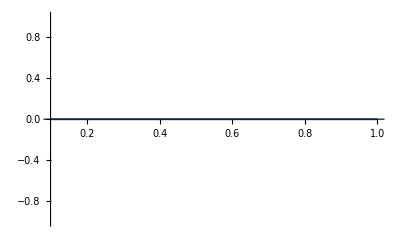

```mathematica
Plot[I*Hdgzall[x,-1],{x,0.1,1}]
```

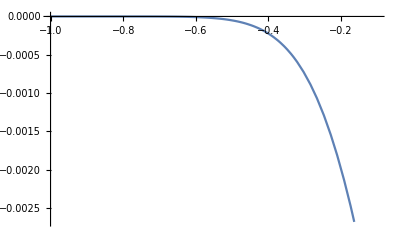

```mathematica
Plot[I*Hdgfall[x,-1],{x,-1,-0.1}]
```

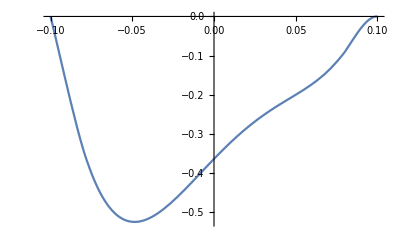

```mathematica
Plot[I*Herallwhole[x,-1],{x,-0.1,0.1}]
```

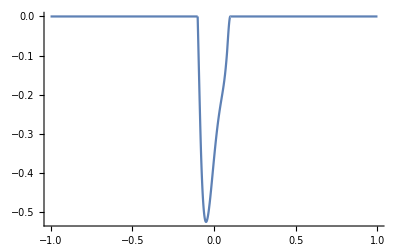

```mathematica
Show[Plot[I*Hdgzall[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Hdgfall[x,-1],{x,-1,-0.1},PlotRange->All],Plot[I*Herallwhole[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

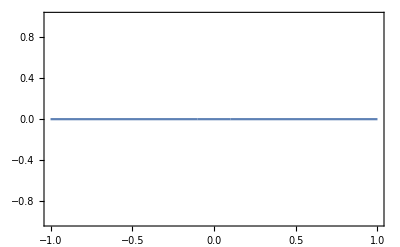
-Graphics-H_uxdiagram j

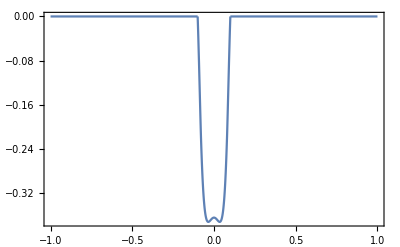
-Graphics-E_uxdiagram j

```mathematica
pHu2d=Labeled[Show[Plot[Hdgzall[x,-1],{x,0.1,1},PlotRange->All],Plot[Hdgfall[x,-1],{x,-1,-0.1},PlotRange->All],Plot[Herallwhole[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_u","x","diagram j"},{Left,Bottom,Top},LabelStyle->24]
pEu2d=Labeled[Show[Plot[Edgzall[x,-1],{x,0.1,1},PlotRange->All],Plot[Edgfall[x,-1],{x,-1,-0.1},PlotRange->All],Plot[Eerallwhole[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_u","x","diagram j"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
pathH=FileNameJoin[{"G:\\calc-online\\gpd\\pic\\gpd-caogao\\717",
"H-f-2d.pdf"}];
pathE=FileNameJoin[{"G:\\calc-online\\gpd\\pic\\gpd-caogao\\717",
"E-f-2d.pdf"}];
```

```mathematica
Export[pathH,pHu2d]
```

G:\calc-online\gpd\pic\gpd-caogao\717\H-f-2d.pdf

```mathematica
Export[pathE,pEu2d]
```

G:\calc-online\gpd\pic\gpd-caogao\717\E-f-2d.pdf

```mathematica
Herall[-0.07,-1]
```

0.+1.83172 ⅈ

```mathematica
Herf[-0.07,-1]
```

0.-0.150458 ⅈ

```mathematica
Hdaf[-0.07,-1]
```

0.-0.234103 ⅈ

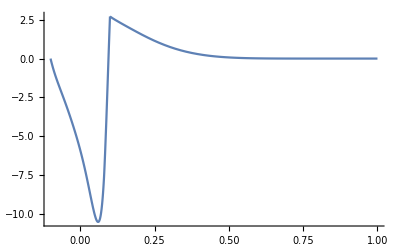

```mathematica
Show[Plot[I*Hdgall[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

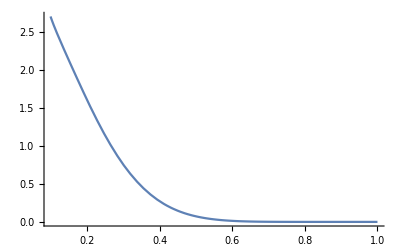

```mathematica
Plot[I*Hdgall[x,-1],{x,0.1,1},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0999959,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

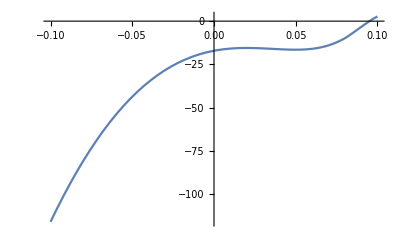

```mathematica
Plot[I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All]
```

```mathematica
p1Hdg
```

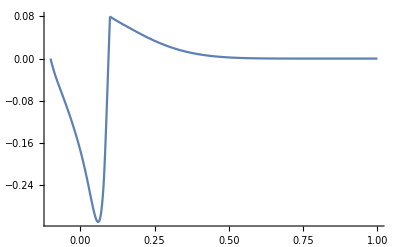

```mathematica
Show[Plot[I*p1Hdg[x,-1],{x,0.1,1},PlotRange->All],Plot[I*p1Her[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
(*d quark*)
```

```mathematica
(*npi+,dbar=u，所以之后再对dbar反转得到d*)
(*pi+的dbar贡献就是u，反转*)
p1Hdgd[x_,t_]=-p1Hdg[-x,t];
p1Herd[x_,t_]=-p1Her[-x,t];

p1Edgd[x_,t_]=-p1Edg[-x,t];
p1Eerd[x_,t_]=-p1Eer[-x,t];


(*pi0,u=d，所以直接套用u的形式*)
(*图的总结果，就是对粒子求和*)
Hdgzalld[x_,t_]=p0Hdg[x,t];
Hdgfalld[x_,t_]=p1Hdgd[x,t]+p0Hdg0[x,t];
Herallwholed[x_,t_]=p1Herd[x,t]+p0Herre[x,t];
Edgzalld[x_,t_]=p0Edg[x,t];
Edgfalld[x_,t_]=p1Edgd[x,t]+p0Edg0[x,t];
Eerallwholed[x_,t_]=p1Eerd[x,t]+p0Eerre[x,t];
```

-Graphics-H_dxdiagram j

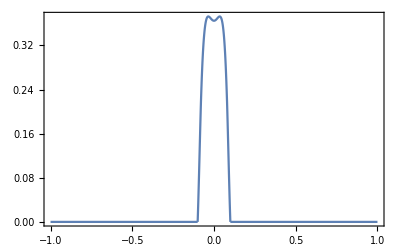
-Graphics-E_dxdiagram j

```mathematica
pHd2d=Labeled[Show[Plot[Hdgzalld[x,-1],{x,0.1,1},PlotRange->All],Plot[Hdgfalld[x,-1],{x,-1,-0.1},PlotRange->All],Plot[Herallwholed[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d","x","diagram j"},{Left,Bottom,Top},LabelStyle->24]
pEd2d=Labeled[Show[Plot[Edgzalld[x,-1],{x,0.1,1},PlotRange->All],Plot[Edgfalld[x,-1],{x,-1,-0.1},PlotRange->All],Plot[Eerallwholed[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d","x","diagram j"},{Left,Bottom,Top},LabelStyle->24]
```